1.222

1.178

8264.46 (0.+1. (-1.2+x))^2.+8265.97 (0.-1. y)^2.

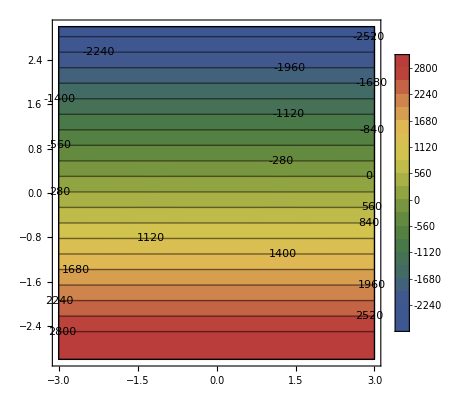

-Graphics-

```mathematica
Clear[size, size2,size2p,size3]
Clear[r1,r2,r3,rt,Xi,z,q]
q=1;
c1=20;
c2=10;
size=3;
size2=Re[zcenter[q]]+2 l1[q]
size2p=(Re[zcenter[q]]-2 l1[q])
size3=2 l2[q];


r1=Re[OmegaFar[q]];
r2=OmegaSQ[q];
r3=Re[OmegaGQ[q]];
rt=Re[TFieldtotal];TMatrix[q];Re[OmegaSQ[q]+Conjugate[gamma]*(z - zcenter[q])*Exp[I*Theta[q]]];(*TMatrix[q];*)
Xi=XiQ[q];
z=x+I y;
r1;
r2;
r3;
rt;
xelipsenormal[q_]:=((x+Re[zcenter[q]]) Cos[Theta[q]]+(y+Im[zcenter[q]]) Sin[Theta[q]])/l1[q]
yelipsenormal[q_]:=((x+Re[zcenter[q]]) Sin[Theta[q]]-(y+Im[zcenter[q]]) Cos[Theta[q]])/l2[q]
(((x-Re[zcenter[q]]) Cos[Theta[q]]+(y-Im[zcenter[q]]) Sin[Theta[q]])/l1[q])^2. + (((x-Re[zcenter[q]]) Sin[Theta[q]]-(y-Im[zcenter[q]])Cos[Theta[q]])/l2[q])^2.

ContourPlot[rt,{x,-size,size},{y,-size,size},BoundaryStyle->Black,RegionFunction->Function[{x,y,z},(((x-Re[zcenter[q]]) Cos[Theta[q]]+(y-Im[zcenter[q]]) Sin[Theta[q]])/l1[q])^2. + (((x-Re[zcenter[q]]) Sin[Theta[q]]-(y-Im[zcenter[q]])Cos[Theta[q]])/l2[q])^2.>=1],ContourLabels->True, Exclusions->None,PlotLegends->Automatic,Exclusions->None,PlotRange->Automatic(*MaxRecursion->4,WorkingPrecision->30,PlotPoints->200*),ColorFunction->"DarkRainbow",Contours->c1]

ContourPlot[r3,{x,-size,size},{y,-size,size},BoundaryStyle->Black,RegionFunction->Function[{x,y,z},(((x-Re[zcenter[q]]) Cos[Theta[q]]+(y-Im[zcenter[q]]) Sin[Theta[q]])/l1[q])^2. + (((x-Re[zcenter[q]]) Sin[Theta[q]]-(y-Im[zcenter[q]])Cos[Theta[q]])/l2[q])^2.<=1],ContourLabels->True, Exclusions->None,PlotLegends->Automatic,Exclusions->None,PlotRange->Automatic(*MaxRecursion->4,WorkingPrecision->30,PlotPoints->200*),ColorFunction->"DarkRainbow",Contours->c2]
```

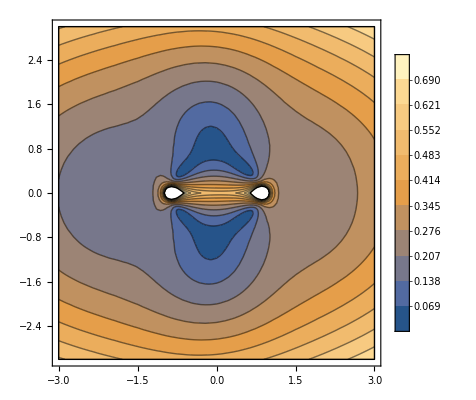

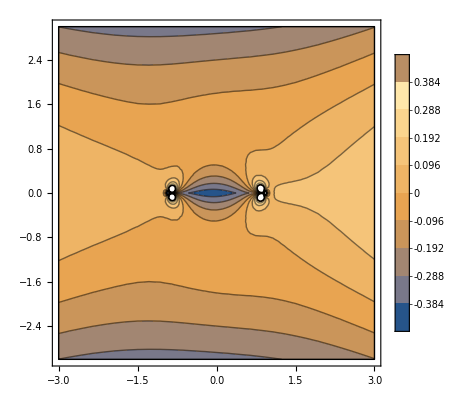

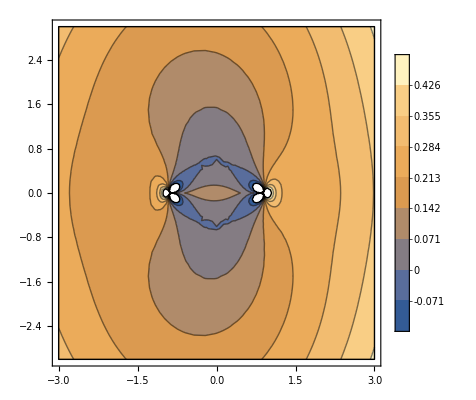

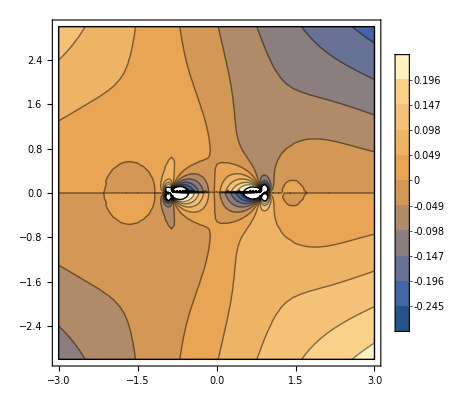

```mathematica
Clear[Sigma11zt,Sigma22zt,Sigma12zt]
Clear[zp,zq,Xi,z]
Sigma11zt[i_]:=Module[{f,f1,f2,f3},f3=Sigma11mStress[i]Cos[Theta[i]]^2-2 Sigma12mStress[i] Cos[Theta[i]] Sin[Theta[i]]+Sigma22mStress[i] Sin[Theta[i]]^2;
f=f3];

Sigma12zt[i_]:=Module[{f,f1,f2,f3},f3=Sigma12mStress[i] Cos[2 Theta[i]]+(Sigma11mStress[i]-Sigma22mStress[i]) Cos[Theta[i]] Sin[Theta[i]];
f=f3];

Sigma22zt[i_]:=Module[{f,f1,f2,f3},f3=Sigma22mStress[i] Cos[Theta[i]]^2+Sigma11mStress[i] Sin[Theta[i]]^2+Sigma12mStress[i] Sin[2 Theta[i]];
f=f3];

Sigma11Ztot[i_]:=Module[{f,f1,f2,f3,f4},Clear[z,zp,zq,Xi];
f1=Sigma11zt[i];
f2=f1;
Xi=XiQ[i];
z=x+I y;
f3=f2]
Sigma12Ztot[i_]:=Module[{f,f1,f2,f3,f4},Clear[z,zp,zq,Xi];
f1=Sigma12zt[i];
f2=f1;
Xi=XiQ[i];
z=x+I y;
f3=f2]
Sigma22Ztot[i_]:=Module[{f,f1,f2,f3,f4},Clear[z,zp,zq,Xi];
f1=Sigma22zt[i];
f2=f1;
Xi=XiQ[i];
z=x+I y;
f3=f2]


Clear[size, size2,size2p,size3,q]
Clear[r11,r12,r22,rt,Xi,z,q,rmv]
c1=10;
c2=4;
q=1;
size=3.;
size2=0Re[zcenter[q]]-1.5* l1[q];
size2p=0Re[zcenter[q]]+1.5* l1[q];
size3=1.5 l2[q];



(*r11=Sigma11Ztot[q]+Sigma11Ztot[q+1];
r12=Sigma12Ztot[q]+Sigma12Ztot[q+1];
r22=Sigma22Ztot[q]+Sigma22Ztot[q+1];*)
(*r11=Sigma11zt[q];
r12=Sigma12zt[q];
r22=Sigma22zt[q];*)
r11=Sigma11m[q];
r12=Sigma12m[q];
r22=Sigma22m[q];
rmv = Sqrt[r11*r11+r22*r22-r11*r22+3r12*r12];




Clear[Xi]
size=3;
Xi=ArcCosh[z/Dq[q]];XiQ[q];
z=x+I y;

ContourPlot[rmv,{x,-size,size},{y,-size,size},BoundaryStyle->Black(*,RegionFunction->Function[{x,y,z},(((x) Cos[Theta[q]]+(y) Sin[Theta[q]])/l1[q])^2. + (((x) Sin[Theta[q]]-(y)Cos[Theta[q]])/l2[q])^2.>=1]*),ContourLabels->False, Exclusions->None,Contours->c1,PlotLegends->Automatic,PlotRange->Automatic]


ContourPlot[r11,{x,-size,size},{y,-size,size},BoundaryStyle->Black,ContourLabels->False, Exclusions->None,Contours->c1,PlotLegends->Automatic,PlotRange->Automatic]



ContourPlot[r22,{x,-size,size},{y,-size,size},BoundaryStyle->Black,ContourLabels->False, Exclusions->None,Contours->c1,PlotLegends->Automatic,PlotRange->Automatic]

ContourPlot[r12,{x,-size,size},{y,-size,size},BoundaryStyle->Black,ContourLabels->False, Exclusions->None,Contours->c1,PlotLegends->Automatic,PlotRange->Automatic]
```

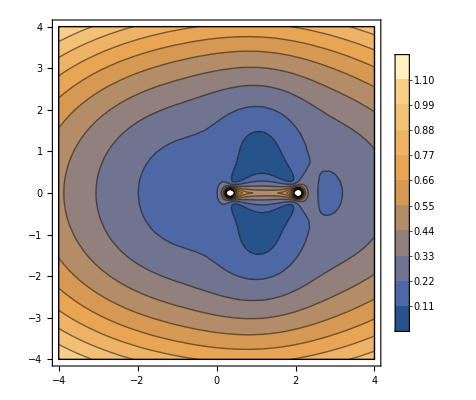

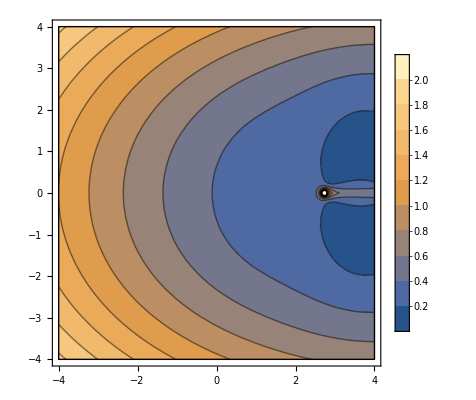

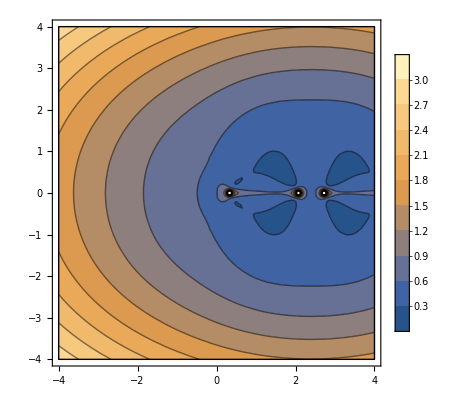

```mathematica
Clear[r111,r112,r11,r121,r122,r12,r221,r222,r22,rmv,rmv1,rmv2]

r111=Sigma11Ztot[1];
r121=Sigma12Ztot[1];
r221=Sigma22Ztot[1];
rmv1 = Sqrt[r111*r111+r221*r221-r111*r221+3r121*r121];

ContourPlot[rmv1,{x,-size,size},{y,-size,size},BoundaryStyle->Black(*,RegionFunction->Function[{x,y,z},(((x) Cos[Theta[q]]+(y) Sin[Theta[q]])/l1[q])^2. + (((x) Sin[Theta[q]]-(y)Cos[Theta[q]])/l2[q])^2.>=1]*),ContourLabels->False, Exclusions->None,Contours->c1,PlotLegends->Automatic,PlotRange->Automatic]


r112=Sigma11Ztot[2];
r122=Sigma12Ztot[2];
r222=Sigma22Ztot[2];
rmv2= Sqrt[r112*r112+r222*r222-r112*r222+3r122*r122];

ContourPlot[rmv2,{x,-size,size},{y,-size,size},BoundaryStyle->Black(*,RegionFunction->Function[{x,y,z},(((x) Cos[Theta[q]]+(y) Sin[Theta[q]])/l1[q])^2. + (((x) Sin[Theta[q]]-(y)Cos[Theta[q]])/l2[q])^2.>=1]*),ContourLabels->False, Exclusions->None,Contours->c1,PlotLegends->Automatic,PlotRange->Automatic]


Clear[Xi]
r11=r111+r112;
r12=r121+r122;
r22=r221+r222;
rmv = Sqrt[r11*r11+r22*r22-r11*r22+3r12*r12];



ContourPlot[rmv,{x,-size,size},{y,-size,size},BoundaryStyle->Black(*,RegionFunction->Function[{x,y,z},(((x) Cos[Theta[q]]+(y) Sin[Theta[q]])/l1[q])^2. + (((x) Sin[Theta[q]]-(y)Cos[Theta[q]])/l2[q])^2.>=1]*),ContourLabels->False, Exclusions->None,Contours->c1,PlotLegends->Automatic,PlotRange->Automatic]
```

```mathematica
Table[Theta[i],{i,ntot}]
Table[l1[i],{i,ntot}]
Table[l2[i],{i,ntot}]
Table[zcenter[i],{i,ntot}]
Table[MuQ[i],{i,ntot}]
Table[NuQtemp[[i]],{i,ntot}]
Table[ThermalConductivityQ[i],{i,ntot}]
Table[ThermalExpansionQ[i],{i,ntot}]
```

{0.,0.}

{1.01,1.01}

{0.5,0.5}

{1.2,-1.2}

{0.,0.}

{0.,0.}

{5.×10^-9,5.×10^-9}

{0.006,0.006}

{{-1.92963×10^-16-21.169 ⅈ,-9.59049×10^-16-21.169 ⅈ},{1.11562×10^-16+2.08024 ⅈ,-3.38126×10^-16-2.08024 ⅈ},{-7.48799×10^-17-1.3327 ⅈ,-1.90207×10^-16-1.3327 ⅈ}}

{{7.35647×10^-26+16.1408 ⅈ,-3.45791×10^-16+16.1408 ⅈ},{-1.28941×10^-26-0.48086 ⅈ,-5.73972×10^-17+0.48086 ⅈ},{2.88928×10^-27+0.102846 ⅈ,-1.23044×10^-17+0.102846 ⅈ}}

{{4.87183×10^-17+5.34465 ⅈ,-1.03655×10^-16+5.34465 ⅈ},{-1.14232×10^-17-0.213003 ⅈ,-2.27753×10^-17+0.213003 ⅈ},{2.77797×10^-18+0.0494416 ⅈ,-5.2479×10^-18+0.0494416 ⅈ}}

{{0.+4.38777 ⅈ,0.+4.38777 ⅈ},{0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}}

{{-4.67583-0.0075372 ⅈ,-4.67583+0.00745409 ⅈ},{5.55603×10^-22-0.370071 ⅈ,7.69752×10^-18-0.370071 ⅈ},{-4.86581×10^-22+0.0218619 ⅈ,2.61257×10^-18-0.0219439 ⅈ}}

{{1.57925+0.00249246 ⅈ,1.57925-0.00257557 ⅈ},{3.67038×10^-22+0.0422666 ⅈ,-8.75844×10^-19+0.0422666 ⅈ},{-4.11915×10^-22-0.000885683 ⅈ,-1.02459×10^-19+0.00080366 ⅈ}}

```mathematica
Table[Snq[j,i],{j,n},{i,ntot}]
Table[Gnq[j,i],{j,n},{i,ntot}]
Table[fnq[j,i],{j,n},{i,ntot}]
Table[Fn[j,i],{j,n},{i,ntot}]
Table[bcTem2nq[j,i],{j,n},{i,ntot}]
Table[bcTem1nq[j,i],{j,n},{i,ntot}]
```

{{6.95978×10^-46+2.87732×10^-9 ⅈ,-2.00576×10^-35+2.87732×10^-9 ⅈ},{-5.47333×10^-46+5.80061×10^-20 ⅈ,-8.93307×10^-36-5.80061×10^-20 ⅈ},{4.04408×10^-46-3.93178×10^-20 ⅈ,-5.20094×10^-36-3.93178×10^-20 ⅈ}}

{{1.06133×10^-36+4.38777 ⅈ,1.5142×10^-26+4.38777 ⅈ},{-2.53038×10^-37+2.68169×10^-11 ⅈ,3.28412×10^-27-2.68169×10^-11 ⅈ},{6.24172×10^-38-6.06839×10^-12 ⅈ,7.43164×10^-28-6.06839×10^-12 ⅈ}}

{{1.06133×10^-36+4.38777 ⅈ,1.5142×10^-26+4.38777 ⅈ},{-2.53038×10^-37+2.68169×10^-11 ⅈ,3.28412×10^-27-2.68169×10^-11 ⅈ},{6.24172×10^-38-6.06839×10^-12 ⅈ,7.43164×10^-28-6.06839×10^-12 ⅈ}}

{{0.+4.38777 ⅈ,0.+4.38777 ⅈ},{0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}}

{{0.000233842+9.35369×10^-6 ⅈ,0.000233842-9.35369×10^-6 ⅈ},{1.15268×10^-42+5.06316×10^-6 ⅈ,1.66152×10^-32+5.06316×10^-6 ⅈ},{-5.76342×10^-43+5.63542×10^-15 ⅈ,7.4802×10^-33+5.51326×10^-15 ⅈ}}

{{-0.0000789798-3.15919×10^-6 ⅈ,-0.0000789798+3.15919×10^-6 ⅈ},{-1.3149×10^-43-5.77575×10^-7 ⅈ,-1.89536×10^-33-5.77575×10^-7 ⅈ},{2.22055×10^-44+5.57199×10^-15 ⅈ,-2.88199×10^-34+5.5767×10^-15 ⅈ}}

```mathematica
Print["Snq"]
Clear[p,q]
p=1;q=1;
Table[Snq[j,p],{j,n}]
Table[Snq[j,q],{j,n}]

Print["Gnq"]
Table[Gnq[j,p],{j,0,n}]
Table[Gnq[j,q],{j,0,n}]

Print["fnq"]
Table[fnq[j,p],{j,0,n}]
Table[fnq[j,q],{j,0,n}]

Print["Fn"]
Table[Fn[j,p],{j,0,n}]
Table[Fn[j,q],{j,0,n}]
```

Snq

{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

Gnq

{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

fnq

{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

Fn

{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
Table[bcTem2nq[j,1],{j,n}]
Table[bcTem2nq[j,2],{j,n}]
Table[bcTem2nq[j,2]-bcTem2nq[j,1],{j,n}]
```

{-1.89424×10^-13-3093.53 ⅈ,6.51077×10^-13+5314.06 ⅈ,6.0156×10^-20-1.07979 ⅈ}

```mathematica
Table[bcTem1nq[j,1],{j,n}]
Table[bcTem1nq[j,2],{j,n}]
Table[bcTem1nq[j,2]-bcTem1nq[j,1],{j,n}]
```

{26.3263-0.0422427 ⅈ,-1.46305×10^-17+0.703767 ⅈ,-1.68069×10^-18+0.014026 ⅈ}

{26.3263+0.0421593 ⅈ,3.67038×10^-22+0.703771 ⅈ,-4.11915×10^-22-0.014108 ⅈ}

{0.+0.0844019 ⅈ,1.46309×10^-17+3.9504×10^-6 ⅈ,1.68028×10^-18-0.028134 ⅈ}

```mathematica
Print["a"]
Table[a[i,1],{i,n}]
Table[a[i,2],{i,n}]
Print["b"]
Table[b[i,1],{i,n}]
Table[b[i,2],{i,n}]
Print["c"]
Table[c[i,1],{i,n}]
Table[c[i,2],{i,n}]
Print["d"]
Table[d[i,1],{i,n}]
Table[d[i,2],{i,n}]
```

a

{-6.44786×10^-6+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

{a[1,2],a[2,2],a[3,2]}

b

{-6.44786×10^-6+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

{b[1,2],b[2,2],b[3,2]}

c

{2.05346×10^-9+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

{c[1,2],c[2,2],c[3,2]}

d

{4.52376×10^-6+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

{d[1,2],d[2,2],d[3,2]}

```mathematica
bcTem1vec
bcTem2vec
```

{1.40679+1.47445 ⅈ,0.-33.4554 ⅈ,0.+1080.77 ⅈ}

{-3093.52+1.47445 ⅈ,0.-5.3189×10^6 ⅈ,0.+1080.77 ⅈ}

```mathematica
bcbar
```

{1.40679,-3093.52,-6.44786×10^-6,-6.44786×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,1.47445,1.47445,0.,0.,-33.4554,-5.3189×10^6,0,0,1080.77,1080.77,0,0}

```mathematica
bcbar
```

{6.44375×10^-6,2.57504×10^-6,-6.44786×10^-6,-6.44786×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0,0,0.,0.,0,0}

```mathematica
Dimensions[bcbar]
```

{24}

```mathematica
PhiFarQ[1]
PhiFarQ[2]
```

0.+0. ⅈ

0.+0. ⅈ

```mathematica
PsiFarQ[1]
PsiFarQ[2]
```

0.+0. ⅈ

0.+0. ⅈ

```mathematica
Phi0[1]
Phi0[2]
```

(0.+0. ⅈ)-(3.5637×10^-15-4.52642×10^-33 ⅈ) ⅇ^(-3 Xi)+(4.28969×10^-15-1.04201×10^-32 ⅈ) ⅇ^(-2 Xi)+(0.+1.83385×10^-32 ⅈ) ⅇ^-Xi-(1.33095×10^-15+7.34545×10^-33 ⅈ) (ⅇ^-Xi+ⅇ^Xi)+(2.9121×10^-16+1.44755×10^-33 ⅈ) (ⅇ^(-2 Xi)+ⅇ^(2 Xi))-(6.63954×10^-17+2.91099×10^-34 ⅈ) (ⅇ^(-3 Xi)+ⅇ^(3 Xi))

(0.+0. ⅈ)-(3.78341×10^-16+7.82577×10^-32 ⅈ) ⅇ^(-3 Xi)+(1.61716×10^-15-2.75653×10^-32 ⅈ) ⅇ^(-2 Xi)+(3.03267×10^-14+1.94416×10^-31 ⅈ) ⅇ^-Xi+(1.02509×10^-16+7.27311×10^-33 ⅈ) (ⅇ^-Xi+ⅇ^Xi)+(3.44915×10^-17+3.13303×10^-33 ⅈ) (ⅇ^(-2 Xi)+ⅇ^(2 Xi))+(1.06338×10^-17+1.13604×10^-33 ⅈ) (ⅇ^(-3 Xi)+ⅇ^(3 Xi))

```mathematica
Psi0[1]
Psi0[2]
```

(0.+0. ⅈ)+(1.72329×10^-15-7.55547×10^-33 ⅈ) ⅇ^(-3 Xi)-(2.55282×10^-15-1.26896×10^-32 ⅈ) ⅇ^(-2 Xi)+(2.67773×10^-14-2.17483×10^-32 ⅈ) ⅇ^-Xi+(1.84668×10^-15+3.71287×10^-33 ⅈ) ⅇ^Xi-(5.22561×10^-16+1.02354×10^-33 ⅈ) ⅇ^(2 Xi)+(1.39862×10^-16+1.6318×10^-34 ⅈ) ⅇ^(3 Xi)+(6.09143×10^-15-7.73699×10^-33 ⅈ) ⅇ^(-3 Xi) (-1.72069 ⅇ^-Xi+0.581161 ⅇ^Xi) Csch[Xi]-(4.88824×10^-15-1.18741×10^-32 ⅈ) ⅇ^(-2 Xi) (-1.72069 ⅇ^-Xi+0.581161 ⅇ^Xi) Csch[Xi]-(0.+1.04486×10^-32 ⅈ) ⅇ^-Xi (-1.72069 ⅇ^-Xi+0.581161 ⅇ^Xi) Csch[Xi]-(1.51666×10^-15+8.37037×10^-33 ⅈ) (ⅇ^-Xi-ⅇ^Xi) Csch[Xi] Sinh[0.542727-Xi]+(6.63686×10^-16+3.29906×10^-33 ⅈ) (ⅇ^(-2 Xi)-ⅇ^(2 Xi)) Csch[Xi] Sinh[0.542727-Xi]-(2.26979×10^-16+9.95151×10^-34 ⅈ) (ⅇ^(-3 Xi)-ⅇ^(3 Xi)) Csch[Xi] Sinh[0.542727-Xi]

(0.+0. ⅈ)+(5.68583×10^-16+5.57937×10^-32 ⅈ) ⅇ^(-3 Xi)-(2.43989×10^-15+8.65518×10^-34 ⅈ) ⅇ^(-2 Xi)-(1.50391×10^-14+1.00795×10^-31 ⅈ) ⅇ^-Xi-(1.44081×10^-15+1.57796×10^-31 ⅈ) ⅇ^Xi-(3.54973×10^-16+3.67612×10^-32 ⅈ) ⅇ^(2 Xi)-(9.39034×10^-17+9.9156×10^-33 ⅈ) ⅇ^(3 Xi)+(6.46698×10^-16+1.33766×10^-31 ⅈ) ⅇ^(-3 Xi) (-1.72069 ⅇ^-Xi+0.581161 ⅇ^Xi) Csch[Xi]-(1.8428×10^-15-3.14115×10^-32 ⅈ) ⅇ^(-2 Xi) (-1.72069 ⅇ^-Xi+0.581161 ⅇ^Xi) Csch[Xi]-(1.72791×10^-14+1.10772×10^-31 ⅈ) ⅇ^-Xi (-1.72069 ⅇ^-Xi+0.581161 ⅇ^Xi) Csch[Xi]+(1.16812×10^-16+8.28794×10^-33 ⅈ) (ⅇ^-Xi-ⅇ^Xi) Csch[Xi] Sinh[0.542727-Xi]+(7.86082×10^-17+7.14037×10^-33 ⅈ) (ⅇ^(-2 Xi)-ⅇ^(2 Xi)) Csch[Xi] Sinh[0.542727-Xi]+(3.63527×10^-17+3.88367×10^-33 ⅈ) (ⅇ^(-3 Xi)-ⅇ^(3 Xi)) Csch[Xi] Sinh[0.542727-Xi]

```mathematica
Clear[a01,a02]
a01=Alpha0[1];
a02=Alpha0[2];
Clear[b01,b02]
b01=Beta0[1];
b02=Beta0[2];
```

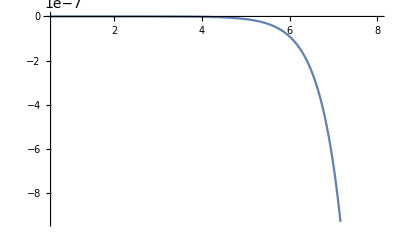

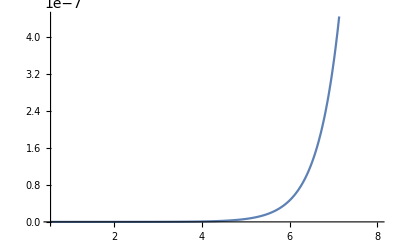

```mathematica
Plot[Re[a01],{Xi,Zeta0[1],8}]
Plot[Re[a02],{Xi,Zeta0[2],8}]
```

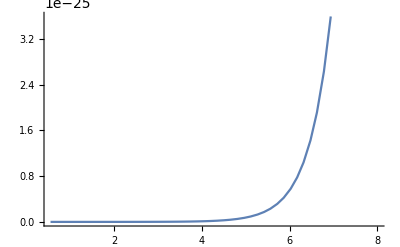

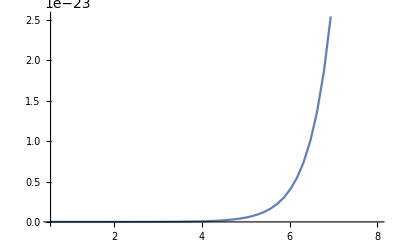

```mathematica
Plot[Im[a01],{Xi,Zeta0[1],8}]
Plot[Im[a02],{Xi,Zeta0[1],8}]
```

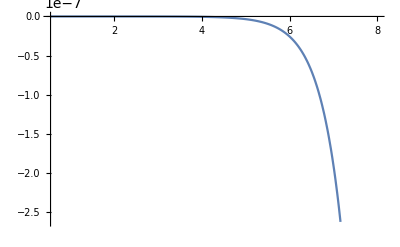

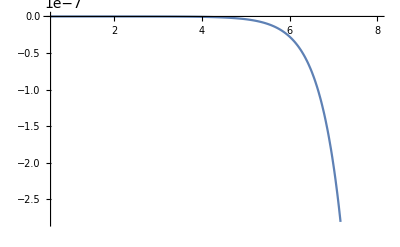

```mathematica
Plot[Re[b01]-Re[a01],{Xi,Zeta0[1],8}]
Plot[Re[b02]-Re[a02],{Xi,Zeta0[2],8}]
```

```mathematica
Clear[f, f1, f2, f3, Phizprim, Phizprimprim, Psizprim , 
      zq, yq ,Omegaprim]
q=2;
Omegaprim = Dq[q] Sinh[Xi];
    Phizprim = D[(Phi0[q]), Xi] / Omegaprim;
    Phizprimprim = D[(Phizprim), Xi] / Omegaprim;
    Psizprim = D[(Psi0[q]), Xi]/Omegaprim;
    f3 = Simplify[
        2.0 Mu0 (Phizprim + 
              Conjugate[Phizprim] - ((Conjugate[yq] - 
                        
            yq) Phizprimprim - Phizprim + Psizprim) )];
    yq = Dq[q] Cosh[Xi]; 
    f = f3;
```

```mathematica
Re[f31-f3]
```

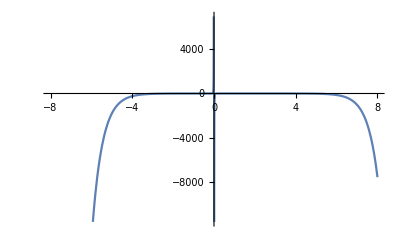

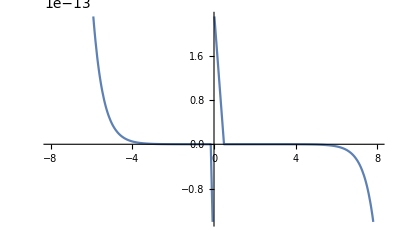

```mathematica
Plot[Re[f31-f3],{Xi,-8,8}]
Plot[Im[f31-f3],{Xi,-8,8}]
```

```mathematica
Clear[PhiQsz,PsiQsz,PhiFarQz,PsiFarQz,Phi0z,Psi0z,Alpha0z,AlphaFar0z,AlphaFarz,Beta00z,Beta0z,BetaFar0z,BetaFarz,z]



PhiQsz[q_] := Module[{f,v}, 
v = Exp[XiQ[q]]; f =  Sum[abmnpq`a[i, q] v^(-i) , {i, n}]] 

PsiQsz[q_] := 
 Module[{f, f1, Psi0, Psi1,v}, 
   v = Exp[XiQ[q]];
  f1 = (Sinh[Zeta0[q]] /Sinh[XiQ[q]]) (v/v0[q] - 
      v0[q]/v); Psi0 = Sum[abmnpq`b[i, q] v^(-i), {i, n}]; 
  Psi1 = Sum[ i f1 abmnpq`a[i, q] v^(-i), {i, n}];
  f = Psi0 - Psi1] 

PhiFarQz[q_] := 
 Module[{f,v}, v = Exp[XiQ[q]]; f =  Sum[faraa[q][[i]] (v^i + v^(-i)) , {i, n}]]

PsiFarQz[q_] := 
 Module[{f, f1, v}, v = Exp[XiQ[q]];
  f1 = (Sinh[Zeta0[q]]*Sinh[XiQ[q] - Zeta0[q]])/(Sinh[XiQ[q]]); 
  f = Sum[(farbb[q][[i]] - 2*i*f1*faraa[q][[i]])*v^(-i) 
     + (farbbminus[q][[i]] + 2*i*f1*faraa[q][[i]])*v^(i), {i, n}]] 

Phi0z:=Module[{f},f=Sum[PhiQsz[p],{p,ntot}]]

Psi0z:=Module[{f},f=Sum[PsiQsz[p],{p,ntot}]]

Alpha0z := 
  Module[{f, f1, f2, f3, Phizprim, Phizprimprim, Psizprim , 
      zq, yq },
    Phizprim = D[(Phi0z), z];
    Phizprimprim = D[(Phizprim), z] ;
    Psizprim = D[(Psi0z), z];
    f3 = Simplify[
        2.0 Mu0 (Phizprim + 
              Conjugate[Phizprim] - ((Conjugate[z] - 
                        
            z) Phizprimprim - Phizprim + Psizprim) )];

    f = f3
    ]

AlphaFar0z[q_] := 
  Module[{f, f1, f2, Phizprim, Phizprimprim, Psizprim, zq , yq },
   
    Phizprim = Simplify[ D[(PhiFarQz[q]), z]];
    Phizprimprim = D[(Phizprim), z] ;
    Psizprim = D[(PsiFarQz[q]), z];
    f1 = 2.0*Mu0*(Phizprim + 
            Conjugate[Phizprim] - ((z - Conjugate[z]) Phizprimprim - Phizprim + Psizprim) ) 
    ]
AlphaFarz[q_] := Module[{f}, f = FullSimplify[AlphaFar0z[q]]]

Alpha0z := 
  Module[{f, f1, f2, f3, Phizprim, Phizprimprim, Psizprim , 
      zq, yq },
    Phizprim = D[(Phi0z), z];
    Phizprimprim = D[(Phizprim), z] ;
    Psizprim = D[(Psi0z), z];
    f3 = Simplify[
        2.0 Mu0 (Phizprim + 
              Conjugate[Phizprim] - ((Conjugate[z] - 
                        
            z) Phizprimprim - Phizprim + Psizprim) )];

    f = f3
    ]

AlphaFar0z[q_] := 
  Module[{f, f1, f2, Phizprim, Phizprimprim, Psizprim, zq , yq },
   
    Phizprim = Simplify[ D[(PhiFarQz[q]), z]];
    Phizprimprim = D[(Phizprim), z] ;
    Psizprim = D[(PsiFarQz[q]), z];
    f1 = 2.0*Mu0*(Phizprim + 
            Conjugate[Phizprim] - ((z - Conjugate[z]) Phizprimprim - Phizprim + Psizprim) ) 
    ]
AlphaFarz[q_] := Module[{f}, f = FullSimplify[AlphaFar0z[q]]]

Beta00z := Module[{f1, f, Phizprim, zq}, 
    
    Phizprim = D[(Phi0z), z] ;
    f = 4 Mu0 Re[(Phizprim + Conjugate[Phizprim])]]

Beta0z := Module[{f}, f = Simplify[Beta00z]]

BetaFar0z[q_] := Module[{f, Phizprim}, 
   
    Phizprim = D[(PhiFarQz[q]), z];
    f = 4 Mu0 Re[(Phizprim + Conjugate[Phizprim])]]
BetaFarz[q_] := Module[{f}, f = FullSimplify[BetaFar0z[q]]]

Clear[Sigma11ztot,Sigma12ztot,Sigma22ztot]
Sigma11ztot:=Module[{f},f=Re[Alpha0z]]
Sigma12ztot:=Module[{f},f=-Im[Alpha0z]]
Sigma22ztot:=Module[{f},f=Beta0z-Re[Alpha0z]]
```

```mathematica
Clear[s11z,s12z,s22z,z,size]
size=4;
s11z=Sigma11ztot;
s12z=Sigma12ztot;
s22z=Sigma22ztot;
z=x+I*y;
s22z;
s12z;
s11z;
smv= Sqrt[s11z*s11z+s22z*s22z-s11z*s22z+3s12z*s12z];
q=1;
c1=10;
size=3;
ContourPlot[smv,{x,-size,size},{y,-size,size},BoundaryStyle->Black,ContourLabels->False, Exclusions->None,PlotLegends->Automatic,MaxRecursion->4,WorkingPrecision->30,Exclusions->None,PlotRange->{-0.0,0.3}(*PlotPoints->200*),ColorFunction->"DarkRainbow",Contours->c1]
```

```mathematica
q=1;q1=2;
Show[ContourPlot[smv,{x,-size,size},{y,-size,size},BoundaryStyle->Black,ContourLabels->False, PlotLegends->Automatic,Exclusions->None,ColorFunction->"DarkRainbow",Contours->c1,PlotRange->Automatic,RegionFunction->Function[{x,y,z},(((x-Re[zcenter[q]]) Cos[Theta[q]]+(y-Im[zcenter[q]]) Sin[Theta[q]])/l1[q])^2. + (((x-Re[zcenter[q]]) Sin[Theta[q]]-(y-Im[zcenter[q]])Cos[Theta[q]])/l2[q])^2.>=1]],ContourPlot[{(((x-Re[zcenter[q1]]) Cos[Theta[q1]]+(y-Im[zcenter[q1]]) Sin[Theta[q1]])/l1[q1])^2. + (((x-Re[zcenter[q1]]) Sin[Theta[q1]]-(y-Im[zcenter[q1]])Cos[Theta[q1]])/l2[q1])^2.==1},{x,size,-size},{y,size,-size},BoundaryStyle->Black,ContourShading->None,ContourLabels->True, Exclusions->None,Contours->c1,ContourStyle->Black]]
(*ContourPlot[s11z,{x,-size,size},{y,-size,size},BoundaryStyle->Black,ContourLabels->True, PlotLegends->Automatic,Exclusions->None,ColorFunction->"DarkRainbow",Contours->c1,RegionFunction->Function[{x,y,z},(((x-Re[zcenter[q]]) Cos[Theta[q]]+(y-Im[zcenter[q]]) Sin[Theta[q]])/l1[q])^2. + (((x-Re[zcenter[q]]) Sin[Theta[q]]-(y-Im[zcenter[q]])Cos[Theta[q]])/l2[q])^2.>=1]]
ContourPlot[s12z,{x,-size,size},{y,-size,size},BoundaryStyle->Black,ContourLabels->False, PlotLegends->Automatic,Exclusions->None,ColorFunction->"DarkRainbow",Contours->c1,RegionFunction->Function[{x,y,z},(((x-Re[zcenter[q]]) Cos[Theta[q]]+(y-Im[zcenter[q]]) Sin[Theta[q]])/l1[q])^2. + (((x-Re[zcenter[q]]) Sin[Theta[q]]-(y-Im[zcenter[q]])Cos[Theta[q]])/l2[q])^2.>=1]]
ContourPlot[s22z,{x,-size,size},{y,-size,size},BoundaryStyle->Black,ContourLabels->False, PlotLegends->Automatic,Exclusions->None,ColorFunction->"DarkRainbow",Contours->c1,RegionFunction->Function[{x,y,z},(((x-Re[zcenter[q]]) Cos[Theta[q]]+(y-Im[zcenter[q]]) Sin[Theta[q]])/l1[q])^2. + (((x-Re[zcenter[q]]) Sin[Theta[q]]-(y-Im[zcenter[q]])Cos[Theta[q]])/l2[q])^2.>=1]]*)
```

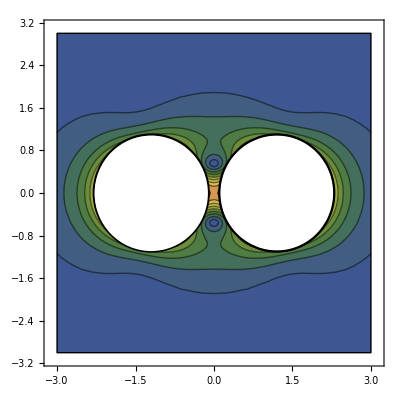

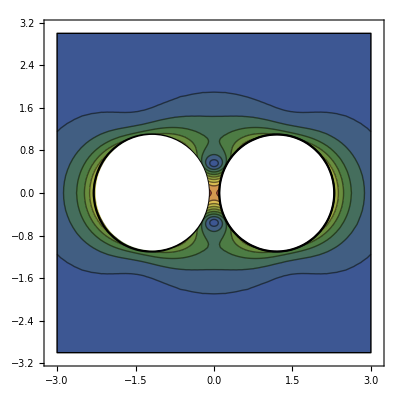

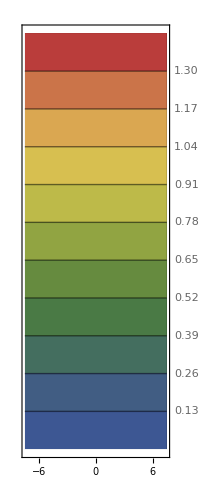

```mathematica
Clear[dminus,PhiQInside,PsiQInside,AlphaQ,BetaQ0]
dminus[i_,q_]:=Module[{f},f=abmnpq`d[i,q]-2 i Sinh[2*Zeta0[q]] abmnpq`c[i,q]]
PhiQInside[q_] := Module[{f,v}, 
v = Exp[XiQ[q]]; f =  Sum[abmnpq`c[i, q] (v^i + v^(-i)) , {i, n}]] 

PsiQInside[q_] := 
 Module[{f, f1, Psi0, Psi1,v}, 
   v = Exp[XiQ[q]];
  f1 = (Sinh[Zeta0[q]] /Sinh[XiQ[q]]) (v/v0[q] - v0[q]/v);Psi0 = Sum[(*abmnpq`*)dminus[i, q] v^(i) + abmnpq`d[i, q] v^(-i), {i, n}]; 
  Psi1 = Sum[ i f1 abmnpq`c[i, q] ( v^(-i) - v^(i)), {i, n}];
  f = Psi0 - Psi1] 

AlphaQ[q_] := 
  Module[{f, f1, f2, f3, Phizprim, Phizprimprim, Psizprim , 
      zq, yq },
    Phizprim = D[(PhiQInside[q]), z] ;
    Phizprimprim = D[(Phizprim), z] ;
    Psizprim = D[(PsiQInside[q]), z];
    f3 = Simplify[
        2.0 MuQ[q] (Phizprim + 
              Conjugate[Phizprim] - ((Conjugate[z] - 
                        
            z) Phizprimprim - Phizprim + Psizprim) )];
 
    f = f3
    ]
BetaQ0[q_] := Module[{f1, f, Phizprim, zq}, 
    Phizprim = D[(PhiQInside[q]), z] ;
    f = 4 MuQ[q] Re[(Phizprim + Conjugate[Phizprim])]]

BetaQ[q_] := Module[{f}, f = Simplify[BetaQ0[q]]]
```

```mathematica
Clear[Sigma11zQ,Sigma12zQ,Sigma22zQ]
Sigma11zQ[q_]:=Module[{f},f=Re[AlphaQ[q]]]
Sigma12zQ[q_]:=Module[{f},f=-Im[AlphaQ[q]]]
Sigma22zQ[q_]:=Module[{f},f=BetaQ[q]-Re[AlphaQ[q]]]

Clear[s11Q,s12Q,s22Q,z,size,x,y]
q=1;
size=40;
s11Q=Sigma11zQ[q];
s12Q=Sigma12zQ[q];
s22Q=Sigma22zQ[q];

s22Q;
s12Q;
s11Q;
smvQ= Sqrt[s11Q*s11Q+s22Q*s22Q-s11Q*s22Q+3s12Q*s12Q];
z=x+I*y;
c1=10;

ContourPlot[smvQ,{x,-size,size},{y,-size,size},BoundaryStyle->Black,RegionFunction->Function[{x,y,z},(((x-Re[zcenter[q]]) Cos[Theta[q]]+(y-Im[zcenter[q]]) Sin[Theta[q]])/l1[q])^2. + (((x-Re[zcenter[q]]) Sin[Theta[q]]-(y-Im[zcenter[q]])Cos[Theta[q]])/l2[q])^2.<=1],ContourLabels->False, Exclusions->None,PlotLegends->Automatic,MaxRecursion->4,WorkingPrecision->30,Exclusions->None,PlotRange->Automatic(*PlotPoints->200*),ColorFunction->"DarkRainbow",Contours->c1]
```

-Graphics-

```mathematica
from external fields at the boundary
1:00017,2:0.00038,3:0.00033,4:0.00068,5:0.00053
```

```mathematica
From Internal fields
5: 0.000288
4:0.000388
3:0.000173
2:0.000216
1:0.000429
```

5

(7.07103+7.07103 ⅈ) Cosh[Xi]

0.881377+ⅈ eta

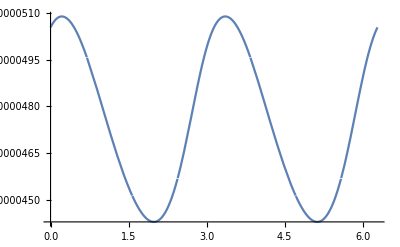

```mathematica
Clear[r,Xi,z,x,y]
q=1;
s11s=Sigma11m[q];
s12s=Sigma12m[q];
s22s=Sigma22m[q];
r=Sqrt[s11s*s11s+s22s*s22s-s11s*s22s+3s12s*s12s];
z=dd[q]Cosh[Xi]
Xi=Zeta0[q]+I*eta

Plot[r,{eta,-0,2Pi}]
```

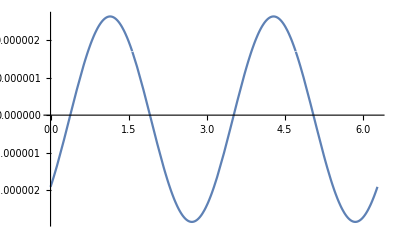

```mathematica
Clear[r,q]
q=5;
r=Tau0[q];
Xi=Zeta0[q]+I*eta;
Plot[r,{eta,-0,2Pi}]
```